```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/y0rkl1u/home/school/ucsd/y1q2-cse291-4/project/egsolver/plots

```mathematica
raw=Transpose[Import["data.csv"]]
```

{{1,11,15,17,23,41,45,46,51,55,95,147},{10,8,10,9,10,9,8,9,9,8,7,10},{3.9,0.3,3.6,0.4,2.6,1.3,0.14,0.7,1.5,0.36,0.05,2.8},{638,65,670,86,436,250,37,164,266,67,20,470},{13.9,0.9,16.2,1.8,9.7,3.4,0.17,1.3,2.9,0.9,0.12,15},{95.8,4,117,9.7,59,21.8,0.56,5.7,18,3.8,0.42,133},{2628,378,3298,505,2046,902,688,380,809,380,50,3295}}

```mathematica
id=raw[[1]];
size=raw[[2]];
baseTime=raw[[3]];
baseMem=raw[[4]];
eggSearchTime=raw[[5]];
eggExtTime=raw[[6]]/(2*3);
eggMem=raw[[7]];
```

```mathematica
plotAndFit[xs_,ys_,xStr_,yStr_,model_]:=(
data=Transpose[{xs,ys}];
fit=Fit[data,model,x];
Show[
ListPlot[data,AxesLabel->{xStr,yStr},
LabelStyle->Directive[Bold],
PlotStyle->PointSize[Medium]
],
Plot[fit,{x,0,Max[xs]},PlotLegends->fit,
PlotStyle->Directive[Pink,Dashed]
]
]
)
```

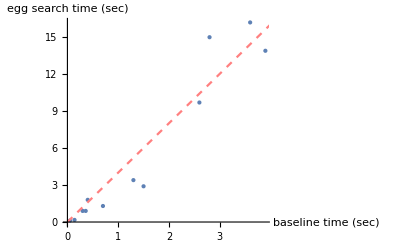

```mathematica
plotAndFit[baseTime,eggSearchTime,"baseline time (sec)","egg search time (sec)",{x}]
```

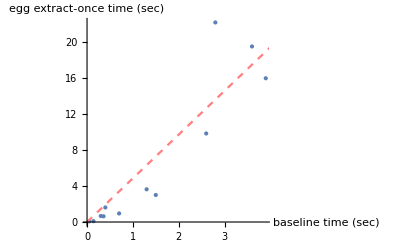

```mathematica
plotAndFit[baseTime,eggExtTime,"baseline time (sec)","egg extract-once time (sec)",{x}]
```

```mathematica
plotAndFit[baseMem,eggMem,"baseline memory (MB)","egg memory (MB)",{x}]
```